This notebook illustrates Example 2 of the paper.

```mathematica
u = {u1, u2}
Xdomain =(-2 <= x1 <= 2 && -2 <= x2 <= 2)
```

{u1,u2}

-2≤x1≤2&&-2≤x2≤2

Define the desired control input and the constraints

```mathematica
Subscript[π, des] = {0, 0}

a1 = {-1, 0}
b1 = -1
a2 = {-1, -x1}
b2 = -1 -x2

Subscript[cons, QP] = {a1.u <= b1, a2.u <= b2}
```

{0,0}

{-1,0}

-1

{-1,-x1}

-1-x2

{-u1≤-1,-u1-u2 x1≤-1-x2}

Define the feasible solution

```mathematica
Subscript[π, f] =  {2 + Abs[x2] ,0}
```

{2+Abs[x2],0}

Check the feasible solution

```mathematica
Simplify[Subscript[cons, QP] /.{u1 -> Subscript[π, f] [[1]], u2 -> Subscript[π, f] [[2]]}, Xdomain]
```

{True,True}

Get the analytic solution to the QP

```mathematica
Subscript[π, qp] = ArgMin[{(u-Subscript[π, des]).(u-Subscript[π, des]), Subscript[cons, QP]}, u]
```

{Piecewise[{{1, (x1==0&&x2≤0)||(x1==-√3&&0<x2≤x1^2)||(x1==-√3&&x2≤0)||(x1==√3&&0<x2≤x1^2)||(x1==√3&&x2≤0)||(x1==&&0<x2≤x1^2)||(x1==&&x2≤0)||(x1>&&x2==x1^2)||(x1>&&0<x2<x1^2)||(x1>&&x2≤0)||(0<x1<√3&&x2==x1^2)||(0<x1<√3&&0<x2<x1^2)||(0<x1<√3&&x2≤0)||(-√3<x1<0&&x2==x1^2)||(-√3<x1<0&&0<x2<x1^2)||(-√3<x1<0&&x2≤0)||(√3<x1<&&x2==x1^2)||(√3<x1<&&0<x2<x1^2)||(√3<x1<&&x2≤0)||(<x1<-√3&&x2==x1^2)||(<x1<-√3&&0<x2<x1^2)||(<x1<-√3&&x2≤0)||(x1≤&&0<x2≤x1^2)||(x1≤&&x2≤0)}, {1+x2, x1==0&&x2>0}, {(1+x2)/(1+x1^2), True}}],Piecewise[{{-√(x2^2/x1^2), (x1==-√3&&0<x2≤x1^2)||(-√3<x1<0&&0<x2<x1^2)||(<x1<-√3&&0<x2<x1^2)||(x1≤&&0<x2≤x1^2)}, {√(x2^2/x1^2), (x1==√3&&0<x2≤x1^2)||(x1==&&0<x2≤x1^2)||(x1>&&0<x2<x1^2)||(0<x1<√3&&0<x2<x1^2)||(√3<x1<&&0<x2<x1^2)}, {-√((-x1^2+2 x2+x2^2)/(1+x1^2)), (-√3<x1<0&&x2==x1^2)||(<x1<-√3&&x2==x1^2)}, {√((-x1^2+2 x2+x2^2)/(1+x1^2)), (x1>&&x2==x1^2)||(0<x1<√3&&x2==x1^2)||(√3<x1<&&x2==x1^2)}, {-√((x1^2+2 x1^2 x2+x1^2 x2^2)/((1+x1^2)^2)), (x1==-√3&&x2>x1^2)||(-√3<x1<0&&x2>x1^2)||(<x1<-√3&&x2>x1^2)||(x1≤&&x2>x1^2)}, {√((x1^2+2 x1^2 x2+x1^2 x2^2)/((1+x1^2)^2)), (x1==√3&&x2>x1^2)||(x1==&&x2>x1^2)||(x1>&&x2>x1^2)||(0<x1<√3&&x2>x1^2)||(√3<x1<&&x2>x1^2)}, {0, True}}]}

```mathematica
FullSimplify[Subscript[π, qp], (Xdomain && x2 <= 1/2 x1^2)]
```

{1,Piecewise[{{x2/x1, x2>0}, {0, True}}]}

```mathematica
Plot3D[Subscript[π, qp][[1]], {x1, -2, 2}, {x2, -2, 2}, AxesLabel->{"x_1","x_2", "u_1"}]
Plot3D[Subscript[π, qp][[2]], {x1, -2, 2}, {x2, -2, 2}, AxesLabel->{"x_1","x_2", "u_2"}]
```

-Graphics3D-

-Graphics3D-

To see the nonlipschitzness, lets focus around x_1 = 0

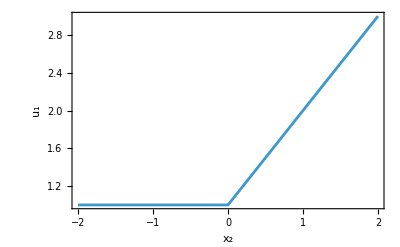

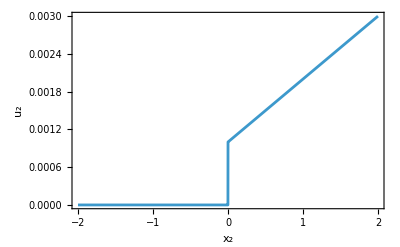

```mathematica
Plot[Subscript[π, qp][[1]]/.x1-> 10^(-3), {x2, -2, 2}, Frame->True, FrameLabel->{"x_2", "u_1"}]
Plot[Subscript[π, qp][[2]]/.x1-> 10^(-3), {x2, -2, 2}, Frame->True, FrameLabel->{"x_2", "u_2"}]
```

We can see a non-Lipschitz jump in the solution. 

Define the SOCP constraints

```mathematica
MyNorm[x_]:= Sqrt[x.x]
MyNormalize[x_]:= x/MyNorm[x]

r = Min[ (b1 - a1.Subscript[π, f])/MyNorm[a1], (b2- a2.Subscript[π, f])/MyNorm[a2]]
Subscript[cons, socp] = FullSimplify[{Sqrt[(u - Subscript[π, f]).(u - Subscript[π, f])] <= r} , Xdomain]
```

Min[1+Abs[x2],(1-x2+Abs[x2])/(√(1+x1^2))]

{√(u2^2+(2-u1+Abs[x2])^2)≤Min[1+Abs[x2],(1-x2+Abs[x2])/(√(1+x1^2))]}

We can compute the analytic solution first

```mathematica
Subscript[π, socpanalytic] =FullSimplify[ Subscript[π, f] + Min[r, MyNorm[Subscript[π, des] -Subscript[π, f]]] MyNormalize[Subscript[π, des] -Subscript[π, f]], Xdomain]
```

{2+Abs[x2]-Min[1+Abs[x2],(1-x2+Abs[x2])/(√(1+x1^2))],0}

Plot the solutions

```mathematica
Plot3D[Subscript[π, socpanalytic][[1]], {x1, -2, 2}, {x2, -2, 2}, AxesLabel->{"x_1","x_2", "u_1"}]
Plot3D[Subscript[π, socpanalytic][[2]], {x1, -2, 2}, {x2, -2, 2}, AxesLabel->{"x_1","x_2", "u_2"}]
```

-Graphics3D-

-Graphics3D-

Check the behaviour around x_1=0

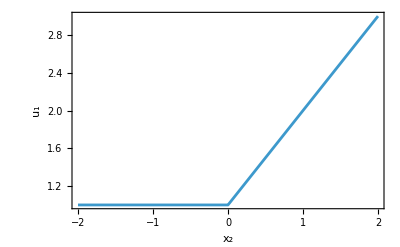

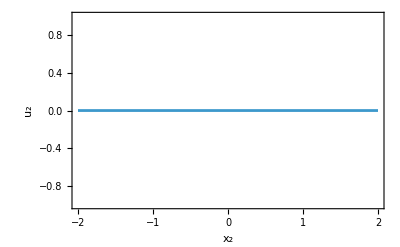

```mathematica
Plot[Subscript[π, socpanalytic][[1]]/.x1-> 10^(-3), {x2, -2, 2}, Frame->True, FrameLabel->{"x_2", "u_1"}]
Plot[Subscript[π, socpanalytic][[2]]/.x1-> 10^(-3), {x2, -2, 2}, Frame->True, FrameLabel->{"x_2", "u_2"}]
```

We can see that the solution of the SOCP is Lipschitz continuous .